```mathematica
$Assumptions = Im[a]==0&&Im[b]==0&&Im[k]==0&&Im[Ω]==0&&Im[l]==0&&(b/k)<a;
```

```mathematica
f1[x_,Ω_] := Evaluate[(Ω*SphericalBesselJ[0, x])/
    (x*(-((SphericalBesselY[0, x]*D[SphericalBesselJ[0, x], {x}])/
        SphericalBesselJ[0, x]) + (Ω*SphericalBesselY[0, x])/x + 
      D[SphericalBesselY[0, x], {x}]))];
```

```mathematica
f2[x_,Ω_] := Evaluate[ArcTan[FullSimplify[f1[x,Ω]]]];
```

```mathematica
delt[Ω_]:=Plot[ArcTan[f1[x,Ω]],{x,0,20},PlotLabel->StringJoin["Ω=",ToString[Ω]],AxesLabel->{"kR","δ_0"},PlotRange->All];
```

```mathematica
amp[Ω_]:=Plot[Sin[x+f2[x,Ω]]/Sin[x],{x,0,20},PlotLabel->StringJoin["Ω=",ToString[Ω]],AxesLabel->{"kR","A_0/D_0"},PlotRange->All];
```

```mathematica
sig[Ω_]:=Plot[4 Pi/(x^2)(Sin[f2[x,Ω]])^2,{x,0,10},PlotLabel->StringJoin["Ω=",ToString[Ω]],AxesLabel->{"kR","σ_0/R^2"},PlotRange->All];
```

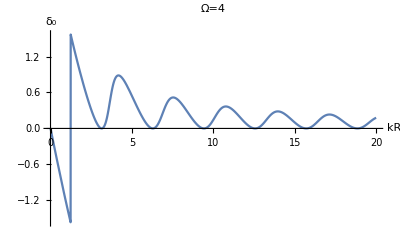

```mathematica
delt[4]
```

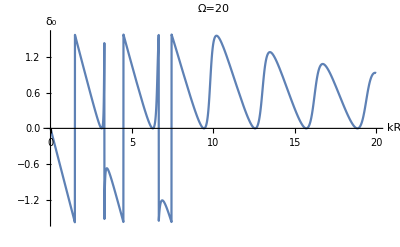

```mathematica
delt[20]
```

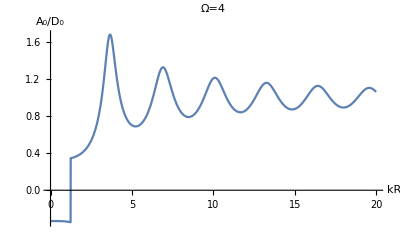

```mathematica
amp[4]
```

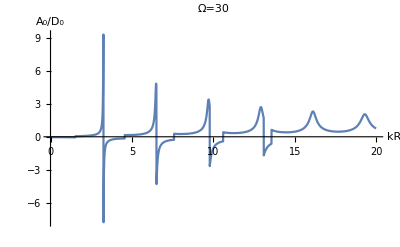

```mathematica
amp[30]
```

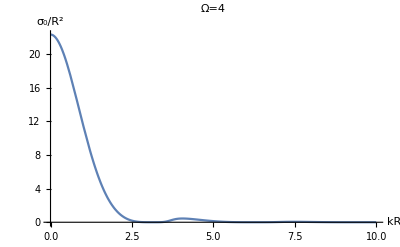

```mathematica
sig[4]
```

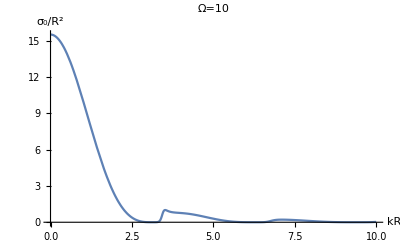

```mathematica
sig[10]
```

```mathematica
f2[x,4]
```

ArcTan[(4 Sin[x]^2)/(x-4 Cos[x] Sin[x])]

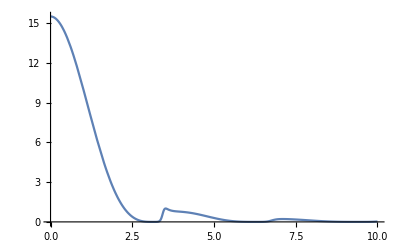

```mathematica
Plot[4 Pi/(x^2)(Sin[ArcTan[(10 Sin[x]^2)/(x-10 Cos[x] Sin[x])]])^2,{x,0,10},PlotRange->All]
```

```mathematica
f3[x_]:=√(k^2-b^2/x^2);
```

```mathematica
Assuming[Im[a]==0&&a>0&&Im[b]==0&&b>0&&Im[k]==0&&k>0&&b^2/k^2<a^2,∫_(b/k)^a -f3[r]ⅆr]
```

-√(-b^2+a^2 k^2)+(b π)/2-b ArcTan[b/(√(-b^2+a^2 k^2))]

```mathematica
-√(a^2 k^2-b^2)+b (-tan^-1(b/(√(a^2 k^2-b^2))))+(π b)/2//FullSimplify
```

-√(-b^2+a^2 k^2)+(b π)/2-b ArcTan[b/(√(-b^2+a^2 k^2))]

```mathematica
deltw[l_,x_]:= Pi/2*Sqrt[l(l+1)]-Sqrt[x^2-l(l+1)]-l(l+1)*ArcTan[Sqrt[l(l+1)]/Sqrt[x^2-l(l+1)]];
```

```mathematica
delte[l_,x_] = ArcTan[SphericalBesselJ[l,x]/SphericalBesselY[l,x]];
```

```mathematica
sigw[l_,x_]:= 4*Pi/(x^2)(2l+1)(Sin[deltw[l,x]])^2;
```

```mathematica
sige[l_,x_]:= 4*Pi/(x^2)(2l+1)(Sin[delte[l,x]])^2;
```

```mathematica
psig[l_]:=Plot[{sige[l,x],sigw[l,x]},{x,l+1, 100},PlotLegends->{"Exact","WKB"},PlotRange->All,AxesLabel->{"k","σ_l"},AxesOrigin->{l+1,0},PlotLabel->StringJoin["l=",ToString[l]]];
```

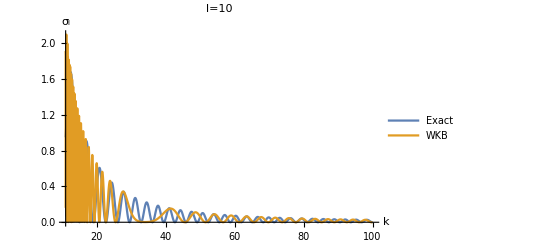

```mathematica
psig[10]
```

```mathematica
Manipulate[Plot[l(l+1)/(x^2),{x,0,20}],{l,0,10,1},PlotRange{{0,20},{0,5}}]
```

Manipulate::vsform: Manipulate argument PlotRange\ {{0, 20}, {0, 5}} does not have the correct form for a variable specification.

```mathematica
Manipulate[Plot[(l (l+1))/x^2,{x,0,20},PlotRange ->{{0,20},{0,5}}],{l,0,10,1}]
```

```mathematica
-
```